# Figure 3: GPS Breeding w/o Post Selection

The conditional position wave-function that results from breeding two GPS states ( created from detecting n photons, optimal squeezing,  and homodyne outcome pTilde) and displacement (δ) in momentum is φTildeκrp.

```mathematica
f[n_,k_]:= Exp[-1/2*2 *Pi/n*pTilde^2]*Sum[(-1)^l*Binomial[n,k]*Binomial[2*k,2*l]*((4*Pi^2*pTilde^2)/n^2)^(k-l)*((4*Pi)/n)^(l+1/2)*Gamma[l+1/2],{l,0,2*k}];
φTildenpδ[n_] := (Exp[-1/2*n/(2*Pi)*q^2]Exp[-I*δ*q]*Sum[f[n,k]*(-1)^j *(Pi/n)^(l+j)*(Factorial[2*(n-k)]/(Factorial[2*(n-k-j-l)]*Factorial[l]*Factorial[j]))*q^(2*(n-k-l-j)),{k,0,n},{l,0,2*(n-k)},{j,0,2*(n-k-l)}])/(Sqrt[Sum[f[n,k]*f[n,kPrime]*((2*Pi)/n)^(2*n-k-kPrime+1/2)*Gamma[2*n-k-kPrime+1/2],{k,0,n},{kPrime,0,n}]]);
```

Given an n and pTilde, the optimal corrective displacement is given by δnp

```mathematica
h[n_,l_]:= 2*Exp[-n/2]*Sum[(-1)^(l-j)*Binomial[2*l,2*j]*(n^2/(4*Pi))^(l-j)*(2*Pi)^(-j-1/2)*Gamma[(3+2*j)/2]*n^((2*j+1)/2)1/(1+2*j),{j,0,2*l}];
g[n_,k_,l_]:=(-1)^(n-k+l)*Binomial[2(n-k),2*l]((4*Pi^2)/n^2)^(n-k-l)*((4*Pi)/n)^(l+1/2)*Gamma[l+1/2];
δnp[n_] :=Arg[ Sum[f[n,k]*f[n,kPrime]*g[n,k,l]*g[n,kPrime,lPrime]*h[n,2*n-k-kPrime-l-lPrime],{k,0,n},{l,0,2*(n-k)},{kPrime,0,n},{lPrime,0,2(n-kPrime)}]/(2*Pi*Sum[f[n,k]*f[n,kPrime]*((2*Pi)/n)^(2*n-k-kPrime+1/2)*Gamma[2*n-k-kPrime+1/2],{k,0,n},{kPrime,0,n}])]/2*Sqrt[Pi];
```

The homodyne probability distribution associated with φTildenpδ is PTildenp.

```mathematica
PTildenp[n_]:=(1/Gamma[n+1/2]*(n/(4*Pi))^n*Sqrt[n]/(2*Pi))^2*Sum[f[n,k]*f[n,kPrime]*((2*Pi)/n)^(2*n-k-kPrime+1/2)*Gamma[2*n-k-kPrime+1/2],{kPrime,0,n},{k,0,n}];
```

The GPS success probabiity, with max probability input squeezing  (r_max) and number of photons detected (n) is given by PGPS.

```mathematica
PGPS[n_]:=(2^-n n^n (1+2 n)^(-1/2-n) Gamma[1+2 n])/(n!)^2;
```

## Generate Data

Points to get data for the following parameters

```mathematica
nSpace= Flatten[{DeleteCases[DeleteCases[Range[7,40],37],39],42}];
pTildeSpaceTable = Range[0,(13 √π)/4,((13 √π)/4-0)/100];
```

Generating Data (Do this on HPC)

```mathematica
(*φTildenpδTable  = ParallelTable[{nSpace[[ii]],Simplify[φTildenpδ[nSpace[[ii]]] ,Assumptions->{pTilde ∈ Reals,q ∈ Reals, δ ∈ Reals}]},{ii,1,Length[nSpace]}];
indx  = Table[Partition[Flatten[Table[{k,l,kPrime,lPrime},{k,0,nSpace[[ii]]},{l,0,2*(nSpace[[ii]]-k)},{kPrime,0,nSpace[[ii]]},{lPrime,0,2(nSpace[[ii]]-kPrime)}]],4],{ii,1,Length[nSpace]}];
γ  = Table[FullSimplify[Total[ParallelTable[f[nSpace[[ii]],indx[[ii,jj,1]]]*f[indx[[ii]],indx[[ii,jj,3]]]*g[nSpace[[ii]],indx[[ii,jj,1]],indx[[ii,jj,2]]]*g[nSpace[[ii]],indx[[ii,jj,3]],indx[[ii,jj,4]]]*h[nSpace[[ii]],2*nSpace[[ii]]-indx[[ii,jj,1]]-indx[[ii,jj,3]]-indx[[ii,jj,2]]-indx[[ii,jj,4]]],{jj,1,Length[indx[[ii]]]}]]],{ii,1,Length[nSpace]}];*)
φTildenpδTable =Get["Figure 5/φTildenpqδTable"];
γ = Get["Figure 5/γ"];
```

Generating Data (Do this on HPC)

```mathematica
γTable = Table[γ[[ii,2]]/.pTilde->pTildeSpaceTable[[jj]],{ii,1,Length[nSpace]},{jj,1, Length[pTildeSpaceTable]}];
δnpTable = Table[Arg[γTable[[ii,jj]]]/(2*Sqrt[Pi]),{ii,1,Length[nSpace]},{jj,1,Length[γTable[[ii]]]},{jj,1, Length[pTildeSpaceTable]}];
φTildenpδTableConj = φTildenpδTable/.δ->-δ;
(*NoErrorPTable=Table[ParallelTable[{pTildeSpaceTable[[jj]],1/Sqrt[Pi]*Sum[Quiet[NIntegrate[Exp[2*I*v*Sqrt[Pi]*(s-t)] (φTildenpδTableConj[[ii,2]]/. {q->2*s*Sqrt[Pi]+u,δ->βTable[[ii,jj]],pTilde->pTildeSpaceTable[[jj]]})*(φTildenpδTable[[ii,2]]/. {q->2*t*Sqrt[Pi]+u,δ->βTable[[ii,jj]],pTilde->pTildeSpaceTable[[jj]]}),{u,-Sqrt[Pi]/6,Sqrt[Pi]/6},{v,-Sqrt[Pi]/6,Sqrt[Pi]/6},Method->"Trapezoidal"]],{t,-1,1},{s,-1,1}]},{jj,1,Length[pTildeSpaceTable]}],{ii,1,Length[nSpace]}];*)
NoErrorPTable = Get["Figure 3/NoErrorPTable"];
```

Find regions of pTilde where NoErrorPTable is greater than a given value ν

```mathematica
νTable=Range[0.335,0.66,(0.66-0.335)/32];
```

```mathematica
FilterdPosition1aTable = Table[Flatten[Position[PNoErrorTable[[ii,;;,2]],_?(#<=νTable[[ii]]&)]+1],{ii,1,Length[nSpace]}];
FilterdPosition1bTable = Table[Flatten[Position[PNoErrorTable[[ii,;;,2]],_?(#>=νTable[[ii]]&)]],{ii,1,Length[nSpace]}];
FilterdPosition2aTable = Table[FilterdPosition1aTable[[ii,Flatten[Position[Differences[FilterdPosition1aTable[[ii]]],_?(#>10&)]]]],{ii,1,Length[nSpace]}];
FilterdPosition2bTable = Table[FilterdPosition1bTable[[ii,Flatten[Position[Differences[FilterdPosition1bTable[[ii]]],_?(#>10&)]]]],{ii,1,Length[nSpace]}];
FilterdPosition2Table = Table[Sort[Flatten[{FilterdPosition2aTable[[ii]], FilterdPosition2bTable[[ii]]}]],{ii,1,Length[nSpace]}];
```

Determine integration limits

```mathematica
IntLimsTable = Table[If[ii<30,Partition[Flatten[{Reverse[-Partition[Flatten[{0,PNoErrorTable[[ii,FilterdPosition2Table[[ii]],1]]}],2],{1,2}],Partition[Flatten[{0,PNoErrorTable[[ii,FilterdPosition2Table[[ii]],1]]}],2]}],2],Partition[Flatten[{Reverse[-Partition[Flatten[PNoErrorTable[[ii,FilterdPosition2Table[[ii]],1]]],2],{1,2}],Partition[Flatten[PNoErrorTable[[ii,FilterdPosition2Table[[ii]],1]]],2]}],2]],{ii,1,Length[nSpace]}];
```

Integrate PTildenp over regions where  NoErrorPTable   >   νTable

```mathematica
(*PHomCutoffNoErrorP=Table[Total[ParallelTable[NIntegrate[PTildenp[nSpace[[ii]]],{pTilde,IntLimsTable[[ii,jj,1]],IntLimsTable[[ii,jj,2]]}],{jj,1,Length[IntLimsTable[[ii]]]}]],{ii,1,Length[nSpace]}];*)
PHomCutoffNoErrorP = Get["Figure 3/PHomCutoffNoErrorP"];
```

Factor in probability of generating the GPS state to get total probability

```mathematica
TotalProb = Table[{{νTable[[ii]],PGPS[nSpace[[ii]]]^2*PHomCutoffNoErrorP[[ii]]}},{ii,1,Length[nSpace]}];
```

```mathematica
TotalProb//ScientificForm
```

{{{3.35×10^-1,9.67216×10^-4}},{{3.45156×10^-1,7.80778×10^-4}},{{3.55313×10^-1,6.24992×10^-4}},{{3.65469×10^-1,5.15729×10^-4}},{{3.75625×10^-1,4.29227×10^-4}},{{3.85781×10^-1,3.64289×10^-4}},{{3.95938×10^-1,3.11623×10^-4}},{{4.06094×10^-1,2.69673×10^-4}},{{4.1625×10^-1,2.35201×10^-4}},{{4.26406×10^-1,2.07012×10^-4}},{{4.36563×10^-1,1.83565×10^-4}},{{4.46719×10^-1,1.63774×10^-4}},{{4.56875×10^-1,1.46992×10^-4}},{{4.67031×10^-1,1.32428×10^-4}},{{4.77188×10^-1,1.19978×10^-4}},{{4.87344×10^-1,1.08921×10^-4}},{{4.975×10^-1,9.94677×10^-5}},{{5.07656×10^-1,9.10345×10^-5}},{{5.17813×10^-1,8.35733×10^-5}},{{5.27969×10^-1,7.6923×10^-5}},{{5.38125×10^-1,7.10259×10^-5}},{{5.48281×10^-1,6.56928×10^-5}},{{5.58438×10^-1,6.09741×10^-5}},{{5.68594×10^-1,5.66365×10^-5}},{{5.7875×10^-1,5.26646×10^-5}},{{5.88906×10^-1,4.90799×10^-5}},{{5.99063×10^-1,4.58376×10^-5}},{{6.09219×10^-1,4.28089×10^-5}},{{6.19375×10^-1,4.00808×10^-5}},{{6.29531×10^-1,3.44093×10^-5}},{{6.39688×10^-1,2.71906×10^-5}},{{6.49844×10^-1,2.18477×10^-5}},{{6.6×10^-1,1.75781×10^-5}}}

## Plot Data

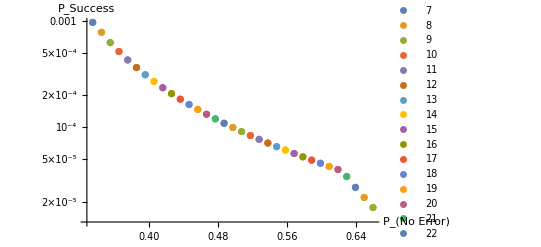

```mathematica
ListLogPlot[TotalProb,AxesLabel->{"P_(No Error)","P_Success"},PlotLegends->Table[ToString[nSpace[[ii]]],{ii,1,Length[nSpace]}]]
```